```mathematica
(*SHO with decaying exponential*)
α = -2;
ω=(α π)/(MM stepSize);
e1[y_]:=ω (Cos[ϕ+ω y]+Sin[ϕ+ω y]);
e2[y_]:=Exp[α N[Pi] NN/MM]ω (Cos[ϕ+ω y]+Sin[ϕ+ω y]);
v[x_,y_]:=Exp[ω x]Sin[ϕ+ω y];
n[x_,y_]:=0;
```

```mathematica
(*Capacitor*)
slope = 1;
e1[y_]:=slope;
e2[y_]:=slope;
v[x_,y_]:=slope(x - NN stepSize);
n[x_,y_]:=0;
```

```mathematica
(*Paraboloid sheet*)
e1[y_]:=-2 NN stepSize;
e2[y_]:=0;
v[x_,y_]:=(x - NN stepSize)^2;
n[x_,y_]:=-2;
```

```mathematica
(*No idea*)
e1[y_]:=(0 - NN stepSize)Sin[ω y];
e2[y_]:=0;
v[x_,y_]:=(x - NN stepSize)^2/2 Sin[ω y];
n[x_,y_]:=Sin[ω y] ((ω^2(x - NN stepSize)^2)/2-1);
```

```mathematica
All of the following are on the decaying SHO
```

```mathematica
Average absolute error per point
25 x 25: 0.03313401620052402
30 x 30: 0.02939258000931582`-2
35 x 35:0.026937572776074104
40 x 40: 0.024774041896402955
45x 45:0.023218882221363115
50 x 50: 0.021892755990561036
55 x 55:0.020882116233775998
60 x 60: 0.019945274434155936
65 x 65:0.019194530533291322
70 x 70: 0.018520911084493136

50 x 40: 0.02729859548213482
40 x 50: 0.019835420072809213
```

```mathematica
30x 30: Precision, Average absolute error per point
6: 0.02939258000931582
7: 0.029392580009315876
8:0.029392580009315876
10:0.029392580009315876
15:0.029392580009315876
20: 0.029392580009315876
```

```mathematica
Average percentage error per point
25 x 25: 14.754701188484455
30 x 30: 10.341350434012668
35 x 35: 10.489817913873713
40 x 40: 5.405166277539816
45 x 45:8.1612577705201
50 x 50: 6.387570784193235
55 x 55:6.744086591390812
60 x 60: 3.8814444422206114
65 x 65:5.749747660158723
70 x 70: 4.705312045047661
```

```mathematica
On paraboloid sheet, absolute error:
55: 658.7999999992841
65: 908.7999999986491
```

```mathematica
Fixed solver running with u=(x - L)^2/2 Sin[ω y]
Sum absolute errors:
25: 3203.7
35: 9222.2
45: 20114.3
55: 37324.2
Sum percentage errors: 
25:121.7
35:200.8
45:286.8
55:377.9
```

0.0285714

{{1/25,3203.8},{1/35,9222.24},{1/45,20114.3},{1/55,37324.2}}

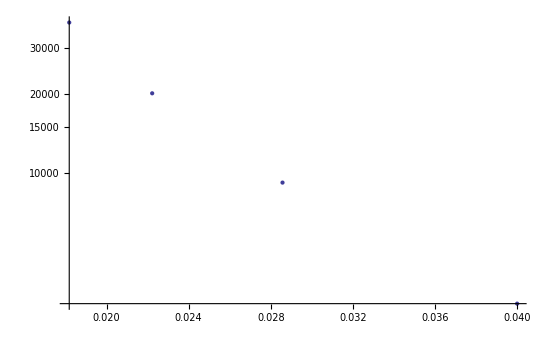

```mathematica
list = {{1/25,3203.7961915481824},{1/35,9222.242582732295},{1/45,20114.311531355725},{1/55,37324.21072551102}}
ListLogPlot[list]
```

{{1/25,5.12607},{1/35,7.52836},{1/45,9.93299},{1/55,12.3386}}

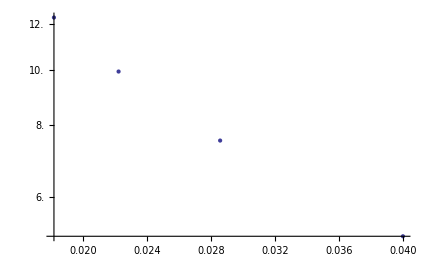

```mathematica
list = {{1/25,3203.7961915481824/25^2},{1/35,9222.242582732295/35^2},{1/45,20114.311531355725/45^2},{1/55,37324.21072551102/55^2}}
ListLogPlot[list]
```

```mathematica
list = {{1/25,0.12492561983471075},{1/35,200.8/35^2},{1/45,286.8/45^2},{1/55,377.9/55^2}}
ListLogPlot[list]
```

{{1/25,0.19472},{1/35,0.163918},{1/45,0.14163},{1/55,0.124926}}

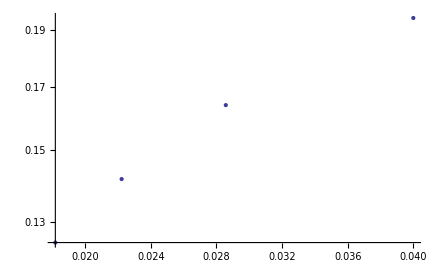

{{1/55,0.0881619},{1/45,0.10162},{1/35,0.12109},{1/25,0.152724}}

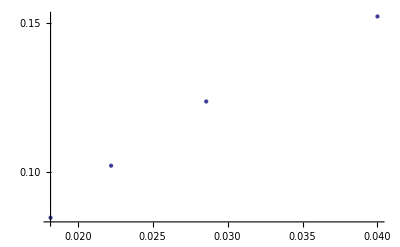

```mathematica
list4={{1/55,0.08816193653716918},{1/45,0.10161978731312298},{1/35,0.12109003755119122},{1/25,0.15272438460294277}}
ListLogPlot[list4]
```

```mathematica
(0.12109003755119122-0.08816193653716918)/(1/35-1/55)
```

3.16933